# Linkage disequilibrium plotting

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Desktop/b-cell-gene-conversion/b-cell-ld

### Plotting

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

```mathematica
numberToString[num_]:=If[Negative[num],"-"<>StringDrop[ToString[num],1],ToString[num]]
```

### Loess fit

```mathematica
LoessFit[(x_)?VectorQ,data_,α_:0.75,λ_:1]:=Table[LoessFit[x[[i]],data,α,λ],{i,Length[x]}]
```

```mathematica
LoessFit[(x_)?NumberQ,data_,α_:0.75,λ_:1]:=WLSFit[data,LoessWts[x,data,α],λ,x];
```

```mathematica
WLSFit[data_,wts_,ldegree_:1,x_]:=Fit[Transpose[(wts*#1&)/@Join[{Table[1,{Length[data]}]},Transpose[data]]],Join[{u},Table[v^i,{i,ldegree}]],{u,v}]/.{u->1,v->x}
```

```mathematica
LoessWts[x_,data_,α_]:=Tricube[(x-First[Transpose[data]])/LoessDistance[x,data,α]]
```

```mathematica
Tricube=Compile[{{x,_Real,1}},If[Abs[#]<1,(1-Abs[#]^3)^3,0]&/@x];
```

```mathematica
LoessDistance[x_,data_,α_]:=Module[{A=Max[1,α],X=First[Transpose[data]],q},q=Min[Length[X],Ceiling[α*Length[X]]];A*Sort[Abs[X-x]][[q]]]
```

## Datasets

```mathematica
datasets={"rPA_day_8","rPA_day_16","rHA_day_16","previous","rabbit","chicken"};
```

```mathematica
descriptions={"tas2016"->"Tas et al. (2016)","rHA_day_16"->"rHA D16","rPA_day_8"->"rPA D8","rPA_day_16"->"rPA D16","rabbit"->"Rabbit GC","chicken"->"Chicken"};
```

## Linkage disequilibrium

```mathematica
linkagePlot[pairs_]:=Module[{points,loess1,fit1,loess2,fit2},
points=ListPlot[pairs,PlotStyle->Directive[AbsolutePointSize[2],Black,Opacity[0.25]],PlotRangePadding->{Scaled[0.01],Scaled[0.02]},PlotRange->{{0,300},{0,1}},Axes->False,Frame->{True,True,False,False},FrameLabel->{"distance (bp)","r^2"},AspectRatio->0.65,ImageSize->300];
loess1=Table[{i,LoessFit[i,pairs,0.1]},{i,0,400,5}];
fit1=ListLinePlot[loess1,PlotStyle->Pink,PlotRange->All];
loess2=Table[{i,LoessFit[i,pairs,0.3]},{i,0,400,5}];
fit2=ListLinePlot[loess2,PlotStyle->Red,PlotRange->All];
Show[points,fit1,fit2]
]
```

```mathematica
plotForDataset[dataset_]:=Module[{data,headers,headerRules,pairs},
data=Import["rsq_tables/rsq_"<>dataset<>".tsv","Table"];
headers=First[data];
headerRules=MapIndexed[#1->#2[[1]]&,headers];
data=Drop[data,1];
pairs=data[[All,{"distance"/.headerRules,"rsq"/.headerRules}]];
Labeled[linkagePlot[pairs],dataset/.descriptions,{{Top,Center}},BaselinePosition->Bottom,Spacings->{0,0},LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12]]
]
```

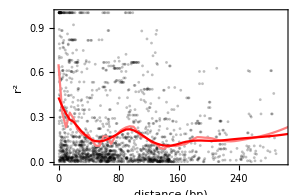
-Graphics-Rabbit GC

```mathematica
plotForDataset["rabbit"]
```

```mathematica
plots=Map[plotForDataset[#]&,datasets];
```

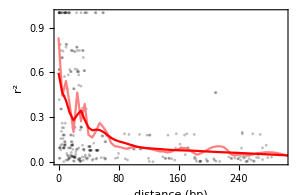
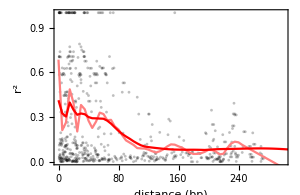
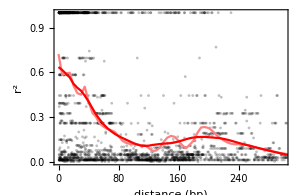
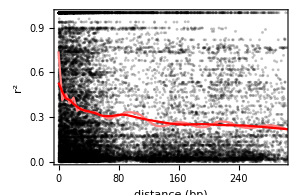
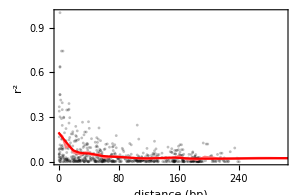
-Graphics-rPA D8 | -Graphics-rPA D16 | -Graphics-rHA D16
-Graphics-previous | -Graphics-Rabbit GC | -Graphics-Chicken

```mathematica
fig=Grid[gappedPartition[plots,3]]
```

```mathematica
Export["figures/ld_plots.png",fig,"PNG",ImageResolution->200]
```

figures/ld_plots.png